```mathematica
(*Derivatives of kernels*)
Krbf[x_,y_,σ_,l_]:=σ^2 ⅇ^(-1/2((x-y)/l)^2)
```

```mathematica
D[Krbf[x,y,σ,l],l]
```

(ⅇ^(-(x-y)^2/(2 l^2)) (x-y)^2 σ^2)/l^3

Log-rbf kernel

```mathematica
Krbflog[x_,y_,σ_,l_]:=Krbf[Log[x],Log[y],σ,l]
```

```mathematica
D[Krbflog[x,y,σ,l],l]
```

(ⅇ^(-(Log[x]-Log[y])^2/(4 l^2)) σ^2 (Log[x]-Log[y])^2)/(2 l^3)

Combined kernel

```mathematica
σm[x_,s_]:=1/(1+ⅇ^(-s(x-0.1)))
D[σm[x,s],s]
```

-(ⅇ^(-s (-0.1+x)) (0.1-x))/((1+ⅇ^(-s (-0.1+x)))^2)

```mathematica
Clear[Krbf,Krbflog,σm]
```

```mathematica
Kcomb[x_,y_,σ1_,l1_,σ2_,l2_,s_]:=σm[x,s]Krbf[x,y,σ1,l1]σm[y,s]+(1-σm[x,s])Krbflog[x,y,σ2,l2](1-σm[y,s])
```

```mathematica
Simplify[D[Kcomb[x,y,σ1,l1,σ2,l2,s],l1]]
```

(ⅇ^(-(x-y)^2/(4 l1^2)) (x-y)^2 σ1^2 σm[x,s] σm[y,s])/(2 l1^3)

```mathematica
D[Kcomb[x,y,σ1,l1,σ2,l2,s],s]
```

-Krbflog[x,y,σ2,l2] (1-σm[y,s]) σm^(0,1)[x,s]+Krbf[x,y,σ1,l1] σm[y,s] σm^(0,1)[x,s]-Krbflog[x,y,σ2,l2] (1-σm[x,s]) σm^(0,1)[y,s]+Krbf[x,y,σ1,l1] σm[x,s] σm^(0,1)[y,s]

```mathematica
aux[x_,s_]:=-(ⅇ^(-s (-0.1+x)) (0.1-x))/((1+ⅇ^(-s (-0.1+x)))^2)
```

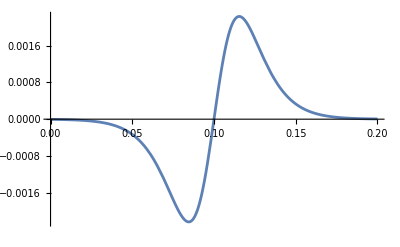

```mathematica
Plot[{aux[x,100]},{x,0,.2}]
```

```mathematica
"interactive plot"%72DynamicModule[{xc,dx},Manipulate[Plot[aux[x,100],{x,xc-dx,xc+dx}],{{xc,0.1,"center"},-0.5000000000000001,0.7000000000000001},{{dx,0.1,"zoom"},0.6000000000000001,0.006000000000000001}],DynamicModuleValues:>{}]
```

Derivatives

```mathematica
Simplify[D[Kcomb[x,y,s1,w1,s2,w2,s],s]]
```

((ⅇ^(s (-0.3+x+2. y)) (0.1-1. x)+ⅇ^(s (-0.3+2 x+y)) (0.1-1. y)+ⅇ^(s (-0.2+x+y)) (-0.2+x+y)) Krbf[x,y,s1,w1]+(ⅇ^(s (-0.1+x)) (-0.1+x)+ⅇ^(s (-0.2+x+y)) (0.2-1. x-1. y)+ⅇ^(s (-0.1+y)) (-0.1+y)) Krbflog[x,y,s2,w2])/((-1.+ⅇ^(s (-0.1+x)))^2 (-1.+ⅇ^(s (-0.1+y)))^2)

Combined kernel

```mathematica
R[z_,t_]:=1/Sqrt[1-2*z*t+t^2]
F[z_,t_,a_,b_]:=1/(R[z,t](1-t+R[z,t])^a R[z,t](1+t+R[z,t])^b)
Kjac[x_,y_,s_,t_,a_,b_]:=s(x*y)^a((1-x)(1-y))^b F[2x-1,t,a,b]F[2y-1,t,a,b]
```

```mathematica
D[Kjac[x,y,s,t,a,b],b]
```

-s (1+t^2-2 t (-1+2 x)) (1-t+1/(√(1+t^2-2 t (-1+2 x))))^-a (1+t+1/(√(1+t^2-2 t (-1+2 x))))^-b ((1-x) (1-y))^b (x y)^a (1+t^2-2 t (-1+2 y)) (1-t+1/(√(1+t^2-2 t (-1+2 y))))^-a (1+t+1/(√(1+t^2-2 t (-1+2 y))))^-b Log[1+t+1/(√(1+t^2-2 t (-1+2 x)))]+s (1+t^2-2 t (-1+2 x)) (1-t+1/(√(1+t^2-2 t (-1+2 x))))^-a (1+t+1/(√(1+t^2-2 t (-1+2 x))))^-b ((1-x) (1-y))^b (x y)^a (1+t^2-2 t (-1+2 y)) (1-t+1/(√(1+t^2-2 t (-1+2 y))))^-a (1+t+1/(√(1+t^2-2 t (-1+2 y))))^-b Log[(1-x) (1-y)]-s (1+t^2-2 t (-1+2 x)) (1-t+1/(√(1+t^2-2 t (-1+2 x))))^-a (1+t+1/(√(1+t^2-2 t (-1+2 x))))^-b ((1-x) (1-y))^b (x y)^a (1+t^2-2 t (-1+2 y)) (1-t+1/(√(1+t^2-2 t (-1+2 y))))^-a (1+t+1/(√(1+t^2-2 t (-1+2 y))))^-b Log[1+t+1/(√(1+t^2-2 t (-1+2 y)))]

```mathematica
Solve[X^2-1==0,X]
```

{{X→-1},{X→1}}

```mathematica
Like[x_,θ_,ϕ_]:=ⅇ^(-nlpEvidence[x,θ,ϕ])
prior[x_,θ_,ϕ_]:=lognormal[x,ϕ]lognormal[x,θ]normal[x,θ]normal[x,ϕ]
post[x_,θ_,ϕ_]:=Like[x,θ,ϕ]prior[x,θ,ϕ]
Potential[x_,θ_,ϕ_]:=-Log[post[x,θ,ϕ]]
Simplify[D[Potential[x,θ,ϕ],ϕ]]
(*PDF[LogNormalDistribution[μ1,σ1]]PDF[LogNormalDistribution[μ,σ]]*)
```

-(lognormal^(0,1)[x,ϕ])/lognormal[x,ϕ]-(normal^(0,1)[x,ϕ])/normal[x,ϕ]+nlpEvidence^(0,0,1)[x,θ,ϕ]

```mathematica
Simplify[D[Post[x,θ],θ]]
```

-ⅇ^(-Evi[x,θ]-Evi1[x,θ]-Evi2[x,θ]) (Evi^(0,1)[x,θ]+Evi1^(0,1)[x,θ]+Evi2^(0,1)[x,θ])

```mathematica
Clear[a,b]
D[x^a(1-x)^b,x]
```

a (1-x)^b x^(-1+a)-b (1-x)^(-1+b) x^a

```mathematica
logNormal[x_,σ_,μ_]:=1/(x σ √(2π))ⅇ^((-(Log[x]-μ)^2)/(2 σ^2))
```

```mathematica
Simplify[D[logNormal[x+ϵ,σ,μ],x]]
```

-(ⅇ^(-(μ-Log[x+ϵ])^2/(2 σ^2)) (-μ+σ^2+Log[x+ϵ]))/(√(2 π) (x+ϵ)^2 σ^3)

```mathematica
Simplify[D[logNormal[x+ϵ,σ,μ],σ]]
```

(ⅇ^(-(μ-Log[x+ϵ])^2/(2 σ^2)) (μ^2-σ^2-2 μ Log[x+ϵ]+Log[x+ϵ]^2))/(√(2 π) (x+ϵ) σ^4)

```mathematica
normal[x_,σ_,μ_]:=1/(√(σ 2π))ⅇ^((-(x-μ)^2)/(2 σ^2))
D[normal[x,σ,μ],x]
```

-(ⅇ^(-(x-μ)^2/(2 σ^2)) (x-μ))/(√(2 π) σ^(5/2))

-0.99

-0.99

1/5

-1

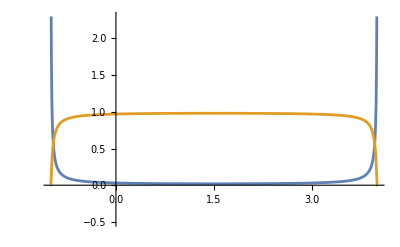

```mathematica
a=-0.99
b=-0.99
m=1/5
b1=-1
Betadist[x_,a_,b_]:=(x^a(1-x)^b)/Beta[a+1,b+1]
Plot[{Betadist[m(x-b1),a,b],ⅇ^(-Betadist[m(x-b1),a,b])},{x,-1,5},PlotRange->{-.5,2.3}]
```

```mathematica
Clear[m,b1,a,b,Betadist]
Simplify[D[ⅇ^(-Betadist[m(x-b1),a,b]),x]]
```

-ⅇ^(-Betadist[m (-b1+x),a,b]) m Betadist^(1,0,0)[m (-b1+x),a,b]

```mathematica
Betadist[x_,a_,b_]:=(x^a(1-x)^b)/Beta[a+1,b+1]
FullSimplify[D[Betadist[x,a,b],x]]
```

-((1-x)^(-1+b) x^(-1+a) (a (-1+x)+b x))/Beta[1+a,1+b]

```mathematica
FullSimplify[D[Betadist[m(x-b1),a,b],x]]
```

-((m (-b1+x))^a (1+b1 m-m x)^(-1+b) (a+a b1 m+b b1 m-(a+b) m x))/((b1-x) Beta[1+a,1+b])

```mathematica
dBeta[x_,a_,b_]:=Betadist[x,a,b](a/x-b/(1-x))
Simplify[dBeta[m(x-b1),a,b]]
```

((m (-b1+x))^a (1+b1 m-m x)^b (a/(m (-b1+x))-b/(1+b1 m-m x)))/Beta[1+a,1+b]